# CCBH coupling and Power Law + Peak

Davi  C. Rodrigues (this code). May, 2023.

```mathematica
ResourceFunction["DarkMode"][]
```

CCBH = Cosmologically coupled Black Hole (arbitrary k value)
DEBH = Dark Energy coupled Black Hole (implies k = - 3w)
m1 = primary (larger) mass of the BBH or NSBH pair.

Naming conventions:
All defined variables/functions start with lower case letter.
“I" at the end of a function name: interpolated version. 
"Raw”: a function without options. It is useful to store results. The version with options is based on the raw version.

## Starting...

```mathematica
(* 
  DIRECTORY STRUCTURE
  *******************
*)

pathBase = NotebookDirectory[];
pathOut = FileNameJoin[{pathBase, "output"}];
pathIn =  FileNameJoin[{pathBase, "input"}];
pathAux = FileNameJoin[{pathBase, "auxiliary"}];

exportOut[fileName_, variable_] := (
  Export[FileNameJoin[{pathOut, fileName}], variable];
  "pathOut/"<>fileName
);
exportAux[fileName_, variable_] := (
  Export[FileNameJoin[{pathAux, fileName}], variable];
  "pathAux/"<>fileName
);
SetAttributes[dumpsave, HoldRest];
dumpsave[fileName_, variable_] := (
  DumpSave[FileNameJoin[{pathAux, fileName}], variable];
  "pathAux/"<>fileName
);
getAux[fileName_] := Get[FileNameJoin[{pathAux, fileName}]];

SetDirectory[pathBase];

(*
  PHYSICAL CONSTANTS
  ******************
*)

(*ΩΛ = 0.6889;*) (*2018 data from Planck*)
(*Ωm = 0.315; (*2018 data from Planck*)
H0Gy = 67.66 / (kpc 10^3) gyr; (*1/Gyr, 2018 data from Planck, 67.66 km/s Mpc^-1*)
*)
Ωm = 0.32;
H0Gy = 70.0 / (kpc 10^3) gyr; (* With these rounded values, the universe age is 13.2 GY*)
gyr = 10^9 60 60 24 365; (*Gyr in seconds*)
kpc = 3.08568 10^16; (*kpc in km*)

(* ------ *)
w0 = -1; (*w0 is the standard value for w, the DE equation of state parameter*)
k0 = 3; (*k0 is the standard growth exponent for CBH.*)
tdmax0 = 13.0; (*Gyrs. The standard maximum delay time. 
13.5 Gyrs from GWTC-3 2111.03634v4 (population paper), but we adopt here a slightly smaller value*)
tdmin0 = 0.05; (*Gyrs. The standard minimum delay time. From GWTC-3 population paper*)
zMax0 = 10; (* Highest redshift where BBH start to form. In accordance with GWTC-3, arXiv:2111.03634v4 (population paper) *)


(*
  META PARAMETERS AND OPTIONS
  ****************************
*)

optionstkw = {
  tdmin -> tdmin0, 
  tdmax -> tdmax0, 
  k -> k0, 
  w -> w0, 
  zMax -> zMax0
};

Clear[baseSimPoints, proportionalBaseSimPoints];
proportionalBaseSimPoints[tdmin_, tdmax_] = Round[(tdmax - tdmin)/(tdmax0 - tdmin0/10) baseSimPoints]; (*The maximum number of realizations is baseSimPoints, 
but this number can get smaller proportionally to tdmax - tdmin. *)
baseSimPoints = 10^6; (*The base number of points to be simmulated for each dimension. *)

(*
  GENERAL PURPOSE FUNCTIONS
  **************************
*)

findSigma::usage = "findSigma[probability] yields the number of σ's for a given probability.";
findSigma[prob_] := Block[{sigma}, 
  sigma /. FindRoot[NProbability[Abs[x] > sigma , x\[Distributed]NormalDistribution[]] == prob, {sigma, 2}]
];

Clear[outSigma];
outSigma[n_] := outSigma[n] = NProbability[Abs[x] > n, x\[Distributed]NormalDistribution[]];

(*
  Calling wl files
  ***************** 
*)

<<"GWTC-3-DataPreparation.wl" 

(* exportOut["plotZxM.pdf", plotZxM] *)

<<"PowerLawPlusPeakDefinition.wl"
```

Event that is in gwPopEvents, but not in gwtcEvents (pos200105):   54

Event that is in gwPopEvents, but not in gwtcEvents (pos190426):   69

datasetGWpop lines to be neglected:   {{9},{16},{54},{69}}

Number of m1 black holes:   72

Use plpp`pi[m, options] for the power-law-plus-peak PDF and plpp`𝒟[options] for the distribution. Use optionsPlpp to see the options.

## Mass factor correction (massFactor)

### Defining cosmology and BBH parameters

```mathematica
Clear[zFormation, hubble, timeZ, w, z];

hubble[z_, w_] = H0Gy Sqrt[Ωm(1+z)^3+(1-Ωm)(1+z)^(3(1+w))]; 

Clear[timeZ];
timeZ[z1_?NumberQ, z2_?NumberQ, w_] := NIntegrate[
  ((1+z) hubble[z, w])^-1, 
  {z, z1, z2}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0}, (*Improves computational time by a factor 5-10, without changes in the answers.*)
  PrecisionGoal -> 5,
  AccuracyGoal -> Infinity,
  MaxRecursion -> 10  (*Removing this may improve speed, it is necessary to check*)
];

zFormation[zObs_?NumberQ, delayTime_?NumberQ, zMax_, w_] := If[
  timeZ[zObs, zMax, w] > delayTime, (*Time between zObs and zMax > td*)
  (*then*)
  FindRoot[
    timeZ[zObs, zformation, w] == delayTime, 
    {zformation, zObs, zMax}, 
    PrecisionGoal -> 5, (*Reminder: AccuracyGoal behaves differently in FindRoot. This is just a minimum precision requirement, probably it will be higher.*)
    Method -> "Brent" (*This is the automatic method for this case, but I am stating it explicitly.*)
  ][[1,2]],
  (*else*)
  zMax  
];

listDelayTime = Range[tdmin0/10, tdmax0, 0.015]; (* delayTime values to be computed. tdmin lower than tdmin0 will be considered*)
listzObs = Range[0.0, 1.0, 0.01];
listw = Range[-1.5, -0.5, 0.1]; 

Clear[minDelayTime, maxDelayTime];
minDelayTime = First[listDelayTime]; (*min delay time to be computed, it can be lower than tdmin0*)
maxDelayTime[zObs_, tdmax_?NumberQ, zMax_?NumberQ, w_] := maxDelayTime[zObs, tdmax, zMax, w] = Min[
  tdmax,
  (*Select[listDelayTime, # <=  tdmax &] // Last, (*essentially, this is the same of tdmax, but it picks a given element of listDelayTime*)*)
  timeZ[zObs, zMax, w]
]; 

massFactor[zObs_,zFormation_, k_] = ((1 + zFormation)/(1 + zObs))^k; (*(a/Subscript[a, i])^k. This is the factor that corrects the mass*)
```

Verifying universe age and the time between z = 10  and today.

```mathematica
Round[timeZ[0, 10^6, w0], 0.1]
timeZ[0,10, w0]
```

13.8

13.2819

```mathematica
maxDelayTime[0.05, tdmax0, zMax0, w0]
```

12.5847

For zMax = 10, the upper limit on t_d < 13.5 Gyrs is useless, since z = 10 corresponds to 13.28 Gyrs.

### Defining zFormationI from a set of computed points.

```mathematica
isComputeTableZformation = False; (*Change to True to compute and regenerate the mx file. About 10 min.*)

If[isComputeTableZformation, 
  Echo["Computing tableZformation..."];
  tableZformation = ParallelTable[
    {{zObs, delayTime, w1}, zFormation[zObs, delayTime, zMax0, w1]}, (*this table uses zMax0, zFornationI can restrict that*)
    {zObs, listzObs},
    {delayTime, listDelayTime}, (*It is computed up to tdmax0*)
    {w1, listw}
  ]; // EchoTiming;
  tableZformationFlat = Flatten[tableZformation, 2];
  dumpsave["tableZformation.mx", tableZformationFlat],
  (*else*)
  getAux["tableZformation.mx"];
  Echo["tableZformation loaded."];
];

Clear[zFormationIraw, zFormationIfast, zFormationI]
zFormationInoZmax[zObs_, delayTime_, w_] = Interpolation[
  tableZformationFlat,
  InterpolationOrder -> 1 
][zObs, delayTime, w]; (*the "I" in the name stands for interpolated. "raw" for no options.*)

(*zFormationIfast[zObs_, delayTime_, opts:OptionsPattern[optionstkw]] = zFormationIraw[zObs, delayTime, OptionValue@w]; *)
(*the "fast" version does not implement the zMax option, thus zMax = zMax0, about 2-3 times faster*)

SetAttributes[zFormationI, Listable]; (*zFormationInoZmax is automatically listable, but the Min function is not Listable*)
zFormationI[zObs_, delayTime_, zMax_, w_] = Min[
  zFormationInoZmax[zObs, delayTime, w],
  zMax
];
```

tableZformation loaded.

Sending zFormationI to the subkernels.

Does not work well. All my tries to parallelize any computation that depends on zFormationI were not successful: interpolating functions in the subkernels are slower than in the kernel.

```mathematica
(*DistributeDefinitions[tableZformationFlat]; (*Takes several seconds.*)
Echo["Distributed."];
ParallelEvaluate[
  zFormationInoZmax[zObs_, delayTime_, w_] = Interpolation[
    tableZformationFlat,
    InterpolationOrder -> 1 
  ][zObs, delayTime, w]
]; (*Takes several seconds*)

ParallelEvaluate[
  SetAttributes[zFormationI, Listable]; (*zFormationInoZmax is automatically listable, but the Min function is not Listable*)
  zFormationI[zObs_, delayTime_, zMax_, w_] = Min[
    zFormationInoZmax[zObs, delayTime, w],
    zMax
  ];
]; (*Quick*)
*)
```

Distributed.

#### Verifying the interpolation

Inspecting the computed points and the interpolation

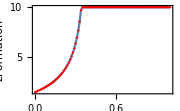
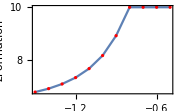
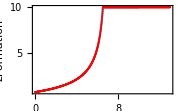
Visually checking the interpolation:   -Graphics--Graphics--Graphics-

```mathematica
originalPlotOptions = Options[Plot];
SetOptions[Plot, Frame -> True, Axes -> False, PlotRange -> All];

Echo[
  Row[{
    Show[
      Plot[zFormationI[zObs, 9, zMax0, w0], 
        {zObs, 0.05, 1.0}, 
        FrameLabel->{"zObs", "zFormation"}
      ], 
      ListPlot[{#, zFormation[#, 9, zMax0, w0]} & /@ listzObs, PlotStyle->Red],
      ImageSize -> Small
    ],
    Show[
      Plot[zFormationI[1, 5, zMax0, w1], 
        {w1, -1.5, -0.5}, 
        FrameLabel->{"w", "zFormation"}
      ], 
      ListPlot[{#, zFormation[1, 5, zMax0, #]} & /@ listw, PlotStyle->Red],
      ImageSize -> Small
    ],
    Show[
      Plot[zFormationI[0.7, delayTime, zMax0, w0], 
        {delayTime, 0.1, 10}, 
        FrameLabel->{"t_d", "zFormation"}
      ], 
      ListPlot[{#, zFormation[0.7, #, zMax0, w0]} & /@ listDelayTime, PlotStyle->Red],
      ImageSize -> Small
    ]
  }],
  "Visually checking the interpolation: "
];
SetOptions[Plot, originalPlotOptions];
```

### The mass factor distribution (𝒟MassFactor & 𝒟InvMassFactor)

ATTENTION: 𝒟MassFactor and dataMassFactor do not work well under paralelization. This is a known issue with computing interpolated function in parallel, and they depend on zFormationI. If zFormatino is used in place, the parallelization works fine, but the improvement of using zFormationI is a factor of ~100, thus parallelizing is not worth. To avoid the issue, I tried doing the interpolatin in the subkernels, but there was no relevant improvement. So I stopped trying to parallel these functions.

```mathematica
ClearAll[
  𝒟MassFactor,
  massFactorDelay, 
  dataMassFactor,
  𝒟InvMassFactor,
  dataDelayTime
];

SetAttributes[massFactorDelay, Listable];
massFactorDelay[zObs_, delayTime_, k_, zMax_, w_] =  massFactor[zObs, zFormationI[zObs, delayTime, zMax, w], k];

randomLogDelayTime[zObs_, tdmin_, tdmax_, zMax_, w_, realizations_] := randomLogDelayTime[zObs, tdmin, tdmax,  zMax, w, realizations] = 
 RandomReal[{Log10[tdmin], Log10 @ maxDelayTime[zObs, tdmax, zMax, w]}, realizations]; (*log-flat distribution.*)

dataDelayTime[zObs_, tdmin_, tdmax_, zMax_, w_] := dataDelayTime[zObs, tdmin, tdmax, zMax, w] = 
 10^randomLogDelayTime[zObs, tdmin, tdmax, zMax, w,  proportionalBaseSimPoints[tdmin, tdmax]]; 

dataMassFactor[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := dataMassFactor[zObs, tdmin, tdmax, k, zMax, w] = 
 massFactorDelay[zObs, dataDelayTime[zObs, tdmin, tdmax, zMax, w], k, zMax, w];
 
𝒟MassFactor[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 𝒟MassFactor[zObs, tdmin, tdmax, k, zMax, w] = SmoothKernelDistribution[
  dataMassFactor[zObs, tdmin, tdmax, k, zMax, w], 
  0.001 (*Manual selection of the band, leads to 0.1% maximum mass precision. Silverman leads to 0.06 for the bandwidth, SheaterJones takes a lot of time and does not converge.*), 
  InterpolationPoints -> 10^4, 
  MaxExtraBandwidths -> {0,0}, 
  PerformanceGoal->"Quality"
];

𝒟InvMassFactor[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 𝒟InvMassFactor[zObs, tdmin, tdmax, k, zMax, w] = SmoothKernelDistribution[
  1/dataMassFactor[zObs, tdmin, tdmax, k, zMax, w], 
  0.001 (*Manual selection of the band, leads to 0.1% maximum mass precision. Silverman leads to 0.06 for the bandwidth, SheaterJones takes a lot of time and does not converge.*), 
  InterpolationPoints -> 10^4, 
  MaxExtraBandwidths -> {0,0}, 
  PerformanceGoal->"Quality"
];
```

#### 𝒟InvMassFactor plot

```mathematica
isCompute𝒟MassFactorCases = False; (*Saved with 2 10^6 realizations*) 

If[isCompute𝒟MassFactorCases, 
  Echo["Computing 𝒟MassFactor 0.05 and 0.9 cases..."];
  𝒟InvMassFactor005 = 𝒟InvMassFactor[0.05, tdmin0, tdmax0, k0, zMax0, w0]; // EchoTiming;
  𝒟InvMassFactor09 = 𝒟InvMassFactor[0.9, tdmin0, tdmax0, k0, zMax0, w0]; // EchoTiming; (*Issue: parallelizing here has several issues, it is quicker this way.*)
  dumpsave["DInvMassFactor005.mx", 𝒟InvMassFactor005];
  dumpsave["DInvMassFactor09.mx", 𝒟InvMassFactor09],
  (*else*)
  getAux["DInvMassFactor005.mx"];
  getAux["DInvMassFactor09.mx"];
  𝒟InvMassFactor[0.05, tdmin0, tdmax0, k0, zMax0, w0] = 𝒟InvMassFactor005;
  𝒟InvMassFactor[0.9, tdmin0, tdmax0, k0, zMax0, w0] = 𝒟InvMassFactor09;
  Echo["𝒟MassFactor 0.05 and 0.9 cases loaded."];
];
```

𝒟MassFactor 0.05 and 0.9 cases loaded.

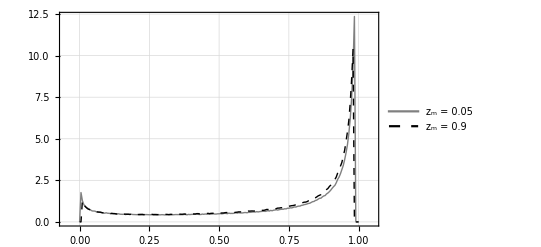

```mathematica
plotInverseMassFactorDistribution = Block[{pdfValues1, pdfValues2},
  pdfValues1 = {#, PDF[𝒟InvMassFactor[0.05, tdmin0, tdmax0, k0, zMax0, w0], #]} & /@ Range[0,1,0.005];
  pdfValues2 = {#, PDF[𝒟InvMassFactor[0.9, tdmin0, tdmax0, k0, zMax0, w0], #]} & /@ Range[0,1,0.005];
  ListPlot[
    {pdfValues1, pdfValues2}, 
    Joined -> True, 
    PlotRange -> {{-0.05,1.05}, All},
    Frame-> True,
    Axes -> False,
    Background->White,
    FrameStyle-> Directive[Black, FontSize -> 13],
    FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
    PlotStyle-> {{Thick, Gray}, {Thick, Dashed, Black}},
    PlotLegends -> Placed[{
      Style["z_m = 0.05", FontFamily->"Times", FontSize -> 15], 
      Style["z_m = 0.9", FontFamily->"Times", FontSize -> 15]},
      {0.2, 0.75}
    ],
    GridLines->Automatic,
    GridLinesStyle->Directive[Dotted, Gray]
  ]
]

(*exportOut["plotInverseMassFactorDistribution.pdf", plotInverseMassFactorDistribution]*)
```

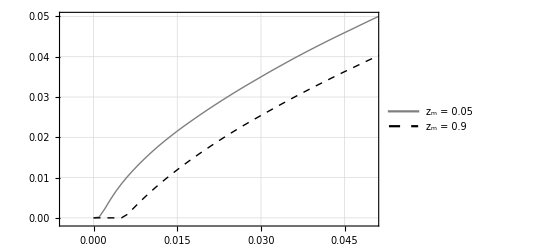

pathOut/plotInverseMassFactorCDF.pdf

```mathematica
plotInverseMassFactorCDF = Block[{cdfValues1, cdfValues2},
  cdfValues1 = {#, CDF[𝒟InvMassFactor[0.05, tdmin0, tdmax0, k0, zMax0, w0], #]} & /@ Range[0,1,0.001];
  cdfValues2 = {#, CDF[𝒟InvMassFactor[0.9, tdmin0, tdmax0, k0, zMax0, w0], #]} & /@ Range[0,1,0.001];
  ListPlot[
    {cdfValues1, cdfValues2}, 
    Joined -> True, 
    PlotRange -> {{-0.005,0.05}, {-0.001, 0.05}},
    Frame-> True,
    Axes -> False,
    Background->White,
    FrameStyle-> Directive[Black, FontSize -> 13],
    FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
    PlotStyle-> {{Thick, Gray}, {Thick, Dashed, Black}},
    PlotLegends -> Placed[{
      Style["z_m = 0.05", FontFamily->"Times", FontSize -> 15], 
      Style["z_m = 0.9", FontFamily->"Times", FontSize -> 15]},
      {0.2, 0.75}
    ],
    GridLines->Automatic,
    GridLinesStyle->Directive[Dotted, Gray]
  ]
]

exportOut["plotInverseMassFactorCDF.pdf", plotInverseMassFactorCDF]
```

## Formation mass distribution

```mathematica
ClearAll[
  dataM1Formation, dataM1FormationRaw,
  𝒟M1Formation, 𝒟M1FormationRaw,
  dataM1Merger
];

𝒟plp = plpp`𝒟[]; (*To use other PLPP parameter values, change here, e.g. 𝒟plp = plpp`𝒟[plpp`dm -> 9];*)
dataM1Merger = RandomVariate[𝒟plp, 2 baseSimPoints] ~ EchoTiming ~ "dataM1Merger";
dataM1FormationRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_]:= dataM1FormationRaw[zObs, tdmin, tdmax, k, zMax, w]= Block[
  {length, dataM1MergerSameLength},
  length = Length @ dataMassFactor[zObs, tdmin, tdmax, k, zMax, w];
  dataM1MergerSameLength = Take[dataM1Merger, length];
  1/dataMassFactor[zObs, tdmin, tdmax, 1, zMax, w]^k dataM1MergerSameLength 
];(*Note that the k=1 inside dataMassFactor, but there is k in the exponent. It's relevant for function memmory, 
such that dataMassFactor needs not to be comptuted again if k changes.*)

dataM1Formation[zObs_, opts:OptionsPattern[optionstkw]] := dataM1FormationRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
]

𝒟M1FormationRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 𝒟M1FormationRaw[zObs, tdmin, tdmax, k, zMax, w] = SmoothKernelDistribution[
  dataM1FormationRaw[zObs, tdmin, tdmax, k, zMax, w],
  0.1, 
  InterpolationPoints -> 10^5, 
  MaxExtraBandwidths -> {0,0}, 
  PerformanceGoal->"Quality"
];

𝒟M1Formation[zObs_, opts:OptionsPattern[optionstkw]] := 𝒟M1FormationRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
];
```

"dataM1Merger"  4.77791

### Plots

```mathematica
dataM1Formation[0.4]; //EchoTiming
dataM1Formation[0.4, k-> 0.5]; //EchoTiming
histFormation3 = Histogram[
  {dataM1Formation[0.4], dataM1Formation[0.4, k-> 0.5], dataM1Merger}, 
  {.2}, 
  "PDF", 
  PlotRange->{{0,50}, All},
  Background->White,
  ChartStyle->{Lighter@Orange, ColorData["AvocadoColors"][0.5], Lighter@Blue},
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  ChartLegends -> Placed[{
    Style["k = 3.0", FontFamily->"Times", FontSize -> 15], 
    Style["k = 0.5", FontFamily->"Times", FontSize -> 15], 
    Style["k = 0.0", FontFamily->"Times", FontSize -> 15]}, 
    {0.8, 0.75}
  ]
]

(*exportOut["histFormation3.pdf", histFormation3]*)
```

0.000029

11.3824

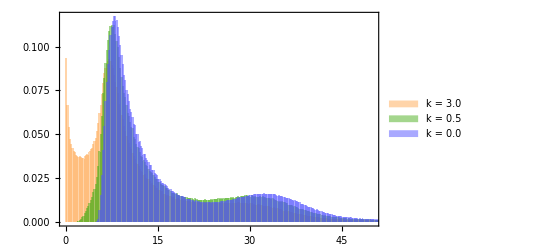

```mathematica
tdmaxE = 5;
tdminE = 0.005;
zMaxE = 2;
𝒟M1Formation[0.4]; //EchoTiming
𝒟M1Formation[0.4, k-> 0.5]; //EchoTiming
𝒟M1Formation[0.4, tdmax -> tdmaxE]; //EchoTiming
𝒟M1Formation[0.4, tdmin -> tdminE]; //EchoTiming
𝒟M1Formation[0.4, zMax -> zMaxE]; //EchoTiming

legend1 = LineLegend[
  {Lighter@Orange, ColorData["AvocadoColors"][0.5], Lighter@Blue}, 
  {
    Style["k=3.0", FontFamily->"Times", FontSize -> 11], 
    Style["k=0.5", FontFamily->"Times", FontSize -> 11], 
    Style["k=0.0", FontFamily->"Times", FontSize -> 11]
  }, 
  LegendMarkerSize -> 20, 
  Spacings -> 0.15 (*It works, although in red*)
];

legend2 = LineLegend[
  {Directive[Lighter@Orange, Dashed], Directive[Lighter@Orange, Dotted], Directive[Lighter@Orange, DotDashed]}, 
  {
    Style["t_max=" <> ToString[Round@tdmaxE]<>" Gyr", FontFamily->"Times", FontSize -> 11], 
    Style["t_min=" <> ToString[Round[10^3 tdminE]]<>" Myr", FontFamily->"Times", FontSize -> 11],
    Style["z_max=" <> ToString[Round[zMaxE]], FontFamily->"Times", FontSize -> 11]
  }, 
  LegendMarkerSize -> 20, 
  Spacings -> 0.15 (*It works, although in red*)
];

tickLarge = 0.015;
tickSmall = 0.006;
frameTicksSmall = Flatten[Table[{n 10^i, "", tickSmall}, {n,1,10}, {i, -4, 0, 1}],1];
frameTicksLarge = Table[{10^i, Superscript[10, i], tickLarge}, {i, -4, 0, 1}];
frameTicksLargeDumb = Table[{10^i, "", tickLarge}, {i, -4, 0, 1}];
frameTicks = Flatten[Join[{frameTicksSmall, frameTicksLarge}],1];
frameTicksDumb = Flatten[Join[{frameTicksSmall, frameTicksLargeDumb}],1];


Off[General::munfl]; 
plotPDFformationDist = LogLogPlot[
  {
    PDF[𝒟M1Formation[0.4], x], 
    PDF[𝒟M1Formation[0.4, tdmax -> tdmaxE], x], 
    PDF[𝒟M1Formation[0.4, tdmin -> tdminE], x], 
    PDF[𝒟M1Formation[0.4, zMax -> zMaxE], x],
    PDF[𝒟M1Formation[0.4, k-> 0.5], x], 
    PDF[𝒟plp, x]
  }, 
  {x, 0.5, plpp`mMax /. optionsPlpp}, 
  PlotRange->{{0.5, 500}, {3 10^-4, .3}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  FrameTicks->{{frameTicks, frameTicksDumb}, {Automatic, Automatic}},
  PlotPoints->2000,
  MaxRecursion->1,
  PlotStyle->{
    {Lighter@Orange}, 
    {Lighter@Orange, Dashed}, 
    {Lighter@Orange, Dotted}, 
    {Lighter@Orange, DotDashed}, 
    {ColorData["AvocadoColors"][0.5]}, 
    {Lighter@Blue}},
  PlotLegends-> {Placed[legend1, {0.60,0.81}], Placed[legend2, {0.85,0.81}]}
]
On[General::munfl];

exportOut["plotPDFformationDist.pdf", plotPDFformationDist]
```

5.×10^-6

0.000018

0.000017

0.000021

0.000019

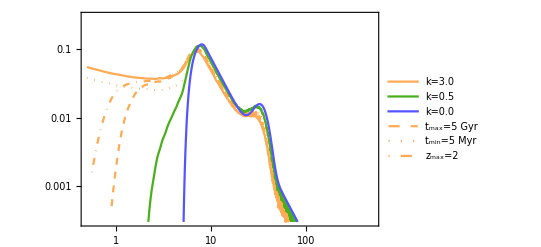

pathOut/plotPDFformationDist.pdf

```mathematica
Superscript[10, 3]
```

10^3

```mathematica
baseSimPoints
```

1000000

## Probabilities for 2<m_th<5 (uses 10^6 Points)

m_th is the threshold mass.

### Computing the relevant distributions

Before the applications, Loading or computing the relevant distributions,

```mathematica
listZobs = (mXzDataForPlotting1 /. Around[x_, y_] -> x)[[All,1]] // Sort;

isComputeTable𝒟M1FormationAllZobs = False; (*Change to True to compute and regenerate the mx file. About 15 min. with (baseSimPoints ~ 10^6)*)

If[isComputeTable𝒟M1FormationAllZobs, 
  Echo["Computing table𝒟M1FormationAllZobs..."];
  tableDM1FormationAllZobs = Table[
    {zObs, 𝒟M1Formation[zObs]}, 
    {zObs, DeleteDuplicates[listZobs]}
  ]; // EchoTiming;
  dumpsave["tableDM1FormationAllZobs.mx", tableDM1FormationAllZobs],
  (*else*)
  getAux["tableDM1FormationAllZobs.mx"];
  (𝒟M1Formation[#1] = #2) & @@@ tableDM1FormationAllZobs;
  Echo["tableDM1FormationAllZobs loaded."];
];
```

tableDM1FormationAllZobs loaded.

### Probabilities related with minimum mass from the above distributions

```mathematica
Clear[listProb, listProbRaw, probabilityMmin, probabilityMminApprox];
listProbRaw[mMin_, tdmin_, tdmax_, k_, zMax_, w_] := listProbRaw[mMin, tdmin, tdmax, k, zMax, w] = 
 NProbability[x>mMin, x \[Distributed] 𝒟M1FormationRaw[#, tdmin, tdmax, k, zMax, w]] & /@  listZobs;
listProb[mMin_, opts:OptionsPattern[optionstkw]] :=  listProbRaw[mMin, OptionValue @ tdmin, OptionValue @ tdmax, OptionValue @ k, OptionValue @ zMax, OptionValue @ w];

probabilityMmin[mMin_, opts:OptionsPattern[optionstkw]] :=  Times @@ listProb[mMin, opts];
probabilityMminApprox[mMin_, opts:OptionsPattern[optionstkw]] := NProbability[x>mMin, x \[Distributed] 𝒟M1Formation[0.4, opts]]^72;

Echo[{probabilityMmin[2], findSigma[probabilityMmin[2]]}, "Probability that the model is correct and the sigma level of rejection: "]; (*taks about 10-15 minutes*)
Echo[{probabilityMminApprox[2], findSigma[probabilityMminApprox[2]]}, "Same as above, for the approximation case: "];
```

Probability that the model is correct and the sigma level of rejection:   {0.000592407,3.43507}

Same as above, for the approximation case:   {0.000659773,3.40577}

Hence, with m_th = 2, the standard CCBH with k =3 is explided at more than 3 σ. Note that the approximation is quite good.

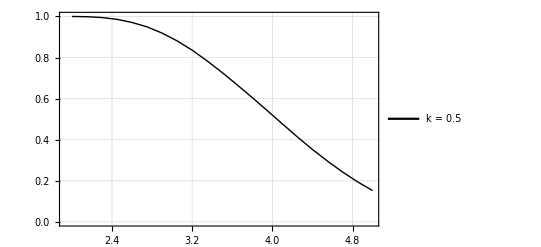

pathOut/plotProbabiliyNull005.pdf

```mathematica
plotProbabiliyNull005 = Block[
  {list = {#, probabilityMminApprox[#, k-> 0.5] } & /@ Range[2,5,0.15]},
  ListPlot[list, 
    Joined->True,
    PlotStyle->{Thick, Black},
    Background->White,
    Frame -> True,
    Axes -> False,
    FrameStyle-> Directive[Black, FontSize -> 13],
    FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
    FrameTicks->{{Automatic, {{outSigma[1], "1σ"}, {outSigma[2], "2σ"}}}, {Automatic, Automatic}},
    GridLines->Automatic,
    GridLinesStyle->Directive[Gray, Dotted],
    PlotLegends-> Placed[{Style["k = 0.5", FontFamily->"Times", FontSize -> 14], Style["k = 1.0", FontFamily->"Times", FontSize -> 14]}, {0.8,0.8}]
  ]
]

exportOut["plotProbabiliyNull005.pdf", plotProbabiliyNull005]
```

```mathematica
list1 = {#, probabilityMminApprox[#]} & /@ Range[2,5,0.5];
list2 = {#, probabilityMminApprox[#, k-> 3 0.9 , w-> -0.9]} & /@ Range[2,5,0.5];
list3 = {#, probabilityMminApprox[#, k-> 3 1.1 , w-> -1.1 ]} & /@ Range[2,5,0.5];
```

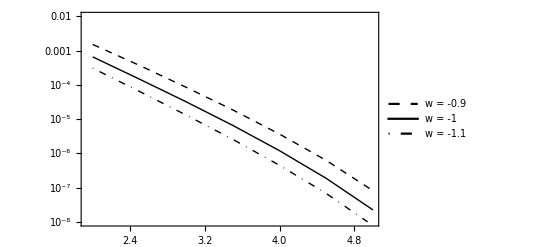

pathOut/plotProbabilityNullw.pdf

```mathematica
plotProbabilityNullw = Block[
  {numbers},
  numbers = Table[{10^-i, StringReplace["10^-a", "a" -> ToString[i]]}, {i, 1, 8, 2}];
  ListLogPlot[{list2, list1, list3}, 
    Joined->True,
    PlotStyle->{{Thick, Dashed, Black}, {Thick, Black}, {Thick, DotDashed, Black}},
    Background->White,
    Frame -> True,
    Axes -> False,
    FrameStyle-> Directive[Black, FontSize -> 13],
    FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
    FrameTicks->{{numbers, {{outSigma[1], "1σ"}, {outSigma[2], "2σ"}, {outSigma[3], "3σ"}, {outSigma[4], "4σ"}, {outSigma[5], "5σ"}}}, {Automatic, Automatic}},
    PlotRange->{All, {10^-8,  10^-2}},
    GridLines->Automatic,
    GridLinesStyle->Directive[Gray, Dotted],
    PlotLegends-> Placed[
      {
        Style["w = -0.9", FontFamily->"Times", FontSize -> 12], 
        Style["w = -1", FontFamily->"Times", FontSize -> 12], 
        Style["w = -1.1", FontFamily->"Times", FontSize -> 12]
      },
      {0.8,0.75}
    ]
  ]
]

exportOut["plotProbabilityNullw.pdf", plotProbabilityNullw]
```

## Confidence plots GBH approach

```mathematica
baseSimPoints = 2 10^5; (*2 10^5 is sufficient here.*)

kValues = {0.5, 0.7, 0.9, 1.1, 1.3, 1.5, 1.7, 1.9, 2.1, 2.3, 2.5, 2.7, 2.9, 3.0}; 
tdmaxValues = Range[3, 13, 1];
tdminValues = {0.005, 0.01, 0.02, 0.03, 0.04, 0.05}; 
zMaxValues = Range[2, 10, 1];
```

### Computing... And defining the probabilities

Order: KT, KZ, KTmin,  TZ, TTmin, ZTmin

```mathematica
isComputeTable𝒟M1KT = False; (*Takes about 4 minutes with baseSimPoints = 2 10^5*)

If[isComputeTable𝒟M1KT, 
  Echo["Computing..."];
  table𝒟M1KT = Table[
    𝒟M1Formation[0.4, k-> k1, tdmax-> tdmax1], 
    {k1, kValues}, 
    {tdmax1, tdmaxValues}
  ]; // EchoTiming;
  dumpsave["tableDM1KT.mx", table𝒟M1KT],
  (*else*)
  getAux["tableDM1KT.mx"];
  Echo["table𝒟M1KT loaded."];
];

tableProbKT = Block[
  {probAux},
  probAux[nk1_, nt1_] := NProbability[x>2, x \[Distributed] table𝒟M1KT[[nk1, nt1]]]^72;
  ParallelTable[
    {{kValues[[nk]], tdmaxValues[[nt]]}, probAux[nk, nt]}, 
    {nk, Length @ kValues}, 
    {nt, Length @ tdmaxValues} 
  ]
]; // AbsoluteTiming
probabilityKT[k_, tdmax_] = Interpolation[Flatten[tableProbKT,1], InterpolationOrder -> 2][k, tdmax];
```

Computing...

257.952

{23.9591,Null}

```mathematica
isComputeTable𝒟M1KZ = False; (*About 5-10 minutes with baseSimPoints = 2 10^5*)

If[isComputeTable𝒟M1KZ, 
  Echo["Computing..."];
  table𝒟M1KZ = Table[
    𝒟M1Formation[0.4, k-> k1, zMax-> zMax1], 
    {k1, kValues}, 
    {zMax1, zMaxValues}
  ]; // EchoTiming;
  dumpsave["tableDM1KZ.mx", table𝒟M1KZ],
  (*else*)
  getAux["tableDM1KZ.mx"];
  Echo["table𝒟M1KZ loaded."];
];

tableProbKZ = Block[
  {probAux},
  probAux[n_, m_] := NProbability[x>2, x \[Distributed] table𝒟M1KZ[[n, m]]]^72;
  ParallelTable[
    {{kValues[[n]], zMaxValues[[m]]}, probAux[n, m]}, 
    {n, Length @ kValues}, 
    {m, Length @ zMaxValues} 
  ]
]; // AbsoluteTiming
probabilityKZ[k_, zMax_] = Interpolation[Flatten[tableProbKZ,1], InterpolationOrder -> 2][k, zMax];
```

{17.1585,Null}

```mathematica
isComputeTable𝒟M1KTmin = False;

If[isComputeTable𝒟M1KTmin, 
  Echo["Computing..."];
  table𝒟M1KTmin = Table[
    𝒟M1Formation[0.4, k-> k1, tdmin-> tdmin1], 
    {k1, kValues}, 
    {tdmin1, tdminValues}
  ]; // EchoTiming;
  dumpsave["tableDM1KTmin.mx", table𝒟M1KTmin],
  (*else*)
  getAux["tableDM1KTmin.mx"];
  Echo["table𝒟M1KTmin loaded."];
];

tableProbKTmin = Block[
  {probAux},
  probAux[n_, m_] := NProbability[x>2, x \[Distributed] table𝒟M1KTmin[[n, m]]]^72;
  ParallelTable[
    {{kValues[[n]], tdminValues[[m]]}, probAux[n, m]}, 
    {n, Length @ kValues}, 
    {m, Length @ tdminValues} 
  ]
]; // AbsoluteTiming
probabilityKTmin[k_, tdmin_] = Interpolation[Flatten[tableProbKTmin,1], InterpolationOrder -> 2][k, tdmin];
```

{12.0739,Null}

```mathematica
isComputeTable𝒟M1TZ = False;

If[isComputeTable𝒟M1TZ, 
  Echo["Computing..."];
  table𝒟M1TZ = Table[
    𝒟M1Formation[0.4, tdmax-> tdmax1, zMax-> zMax1], 
    {tdmax1, tdmaxValues}, 
    {zMax1, zMaxValues}
  ]; // EchoTiming;
  dumpsave["tableDM1TZ.mx", table𝒟M1TZ],
  (*else*)
  getAux["tableDM1TZ.mx"];
  Echo["table𝒟M1TZ loaded."];
];

tableProbTZ = Block[
  {probAux},
  probAux[n_, m_] := NProbability[x>2, x \[Distributed] table𝒟M1TZ[[n, m]]]^72;
  ParallelTable[
    {{tdmaxValues[[n]], zMaxValues[[m]]}, probAux[n, m]}, 
    {n, Length @ tdmaxValues}, 
    {m, Length @ zMaxValues} 
  ]
]; // AbsoluteTiming
probabilityTZ[tdmax_, zMax_] = Interpolation[Flatten[tableProbTZ,1], InterpolationOrder -> 2][tdmax, zMax];
```

Computing...

266.553

{12.359,Null}

```mathematica
isComputeTable𝒟M1TTmin = False;

If[isComputeTable𝒟M1TTmin, 
  Echo["Computing..."];
  table𝒟M1TTmin = Table[
    𝒟M1Formation[0.4, tdmax-> tdmax1, tdmin-> tdmin1], 
    {tdmax1, tdmaxValues}, 
    {tdmin1, tdminValues}
  ]; // EchoTiming;
  dumpsave["tableDM1TTmin.mx", table𝒟M1TTmin],
  (*else*)
  getAux["tableDM1TTmin.mx"];
  Echo["table𝒟M1TTmin loaded."];
];

tableProbTTmin = Block[
  {probAux},
  probAux[n_, m_] := NProbability[x>2, x \[Distributed] table𝒟M1TTmin[[n, m]]]^72;
  ParallelTable[
    {{tdmaxValues[[n]], tdminValues[[m]]}, probAux[n, m]}, 
    {n, Length @ tdmaxValues}, 
    {m, Length @ tdminValues} 
  ]
]; // AbsoluteTiming
probabilityTTmin[tdmax_, tdmin_] = Interpolation[Flatten[tableProbTTmin,1], InterpolationOrder -> 2][tdmax, tdmin];
```

table𝒟M1TTmin loaded.

{6.51817,Null}

```mathematica
isComputeTable𝒟M1ZTmin = False;

If[isComputeTable𝒟M1ZTmin, 
  Echo["Computing..."];
  table𝒟M1ZTmin = Table[
    𝒟M1Formation[0.4, zMax-> zMax1, tdmin-> tdmin1], 
    {zMax1, zMaxValues}, 
    {tdmin1, tdminValues}
  ]; // EchoTiming;
  dumpsave["tableDM1ZTmin.mx", table𝒟M1ZTmin],
  (*else*)
  getAux["tableDM1ZTmin.mx"];
  Echo["table𝒟M1ZTmin loaded."];
];

tableProbZTmin = Block[
  {probAux},
  probAux[n_, m_] := NProbability[x>2, x \[Distributed] table𝒟M1ZTmin[[n, m]]]^72;
  ParallelTable[
    {{zMaxValues[[n]], tdminValues[[m]]}, probAux[n, m]}, 
    {n, Length @ zMaxValues}, 
    {m, Length @ tdminValues} 
  ]
]; // AbsoluteTiming
probabilityZTmin[zMax_, tdmin_] = Interpolation[Flatten[tableProbZTmin,1], InterpolationOrder -> 2][zMax, tdmin];
```

Computing...

208.679

{8.70164,Null}

### Plots

Order: KT, KZ, KTmin,  TZ, TTmin, ZTmin

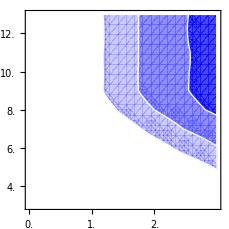

pathOut/regionPlotKT.pdf

```mathematica
largeTick = 0.02;
smallTick = 0.01;
frameTicksK = Table[If[IntegerPart[i]==i, {i/10., i/10., largeTick}, {i/10., "", smallTick}], {i, 0, 27.5, 2.5}];
frameTicksZ = Table[If[IntegerPart[i]==i, {i, i, largeTick}, {i, "", smallTick}], {i, 2.5, 9.5, 0.5}];
frameTicksTmin = Table[If[IntegerPart[i]==i, {i/100, i 10 (*Myr unit*), largeTick}, {i/100, "", smallTick}], {i, 0.5, 4.5, 0.5}];
frameTicksTmax = Table[If[IntegerPart[i]==i, {i, i, largeTick}, {i, "", smallTick}], {i, 3.5, 12.5, 0.5}];

plotSize = 200;
spaceLeft = 30;
spaceBottom = 20;
frameStyle = Directive[Black, FontSize -> 18, Thickness[0.005]];
frameTicksStyle = Directive[Black, FontFamily-> "Times"];
boundaryStyle = {1 -> Directive[White, Thin], 2 -> Directive[White, Thin], 3-> Directive[White, Thin]};
plotStyle = {Directive[Lighter@Blue, Opacity[0.3]], Directive[Lighter@Blue, Opacity[0.5]], Directive[Blue, Opacity[0.5]]};

regionPlotKT = RegionPlot[
  {
    probabilityKT[k,tdmax] < outSigma[1],
    probabilityKT[k,tdmax] < outSigma[2],
    probabilityKT[k,tdmax] < outSigma[3]
  },
  {k, .5, 3}, {tdmax, First@tdmaxValues, tdmax0},
  Background -> White, 
  PlotStyle -> plotStyle,
  BoundaryStyle -> boundaryStyle,
  FrameStyle -> frameStyle,
  FrameTicksStyle -> frameTicksStyle,
  FrameTicks -> {{frameTicksTmax, frameTicksTmax}, {frameTicksK, frameTicksK}},
  PlotRangePadding -> None,
  PlotRange -> {{0,3}, {First@tdmaxValues, tdmax0}},
  ImagePadding -> {{spaceLeft, None}, {None, None}},
  ImageSize -> {plotSize + spaceLeft, plotSize}
]

exportOut["regionPlotKT.pdf", regionPlotKT]
```

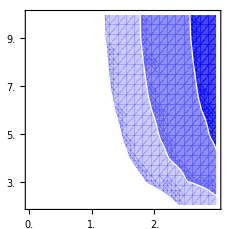

pathOut/regionPlotKZ.pdf

```mathematica
regionPlotKZ = RegionPlot[
  {
    probabilityKZ[k,zMax] < outSigma[1],
    probabilityKZ[k,zMax] < outSigma[2],
    probabilityKZ[k,zMax] < outSigma[3]
  },
  {k, .5, 3}, {zMax, First@zMaxValues, zMax0},
  Background->White, 
  PlotStyle -> plotStyle,
  BoundaryStyle -> boundaryStyle,
  FrameStyle -> frameStyle,
  FrameTicksStyle -> frameTicksStyle,
  FrameTicks->{{frameTicksZ, frameTicksZ}, {frameTicksK, frameTicksK}},
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotRangePadding->None,
  ImagePadding->{{spaceLeft, None}, {None, None}},
  ImageSize->{plotSize + spaceLeft, plotSize},
  PlotRange->{{0,3}, {First@zMaxValues, zMax0}}
]

exportOut["regionPlotKZ.pdf", regionPlotKZ]
```

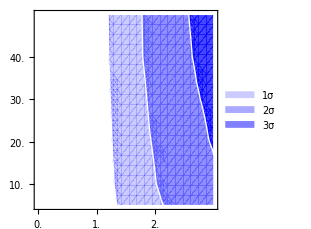

pathOut/regionPlotKTmin.pdf

```mathematica
regionPlotKTmin = RegionPlot[
  {
    probabilityKTmin[k,tdmin] < outSigma[1],
    probabilityKTmin[k,tdmin] < outSigma[2],
    probabilityKTmin[k,tdmin] < outSigma[3]
  },
  {k, .5, 3}, {tdmin, First@tdminValues, tdmin0},
  Background->White, 
  PlotStyle -> plotStyle,
  BoundaryStyle -> boundaryStyle,
  FrameStyle -> frameStyle,
  FrameTicksStyle -> frameTicksStyle,
  FrameTicks -> {{frameTicksTmin, frameTicksTmin},{frameTicksK, frameTicksK}},
  PlotRangePadding -> None,
  ImagePadding->{{spaceLeft, None}, {spaceBottom, None}},
  ImageSize->{plotSize + spaceLeft, plotSize + spaceBottom},
  PlotLegends -> Placed[{
    Style["1σ", FontFamily->"Times", FontSize -> 18], 
    Style["2σ", FontFamily->"Times", FontSize -> 18], 
    Style["3σ", FontFamily->"Times", FontSize -> 18]}, 
    {0.15, 0.18}
  ],
  PlotRange->{{0,3}, {First@tdminValues, tdmin0}}
]

exportOut["regionPlotKTmin.pdf", regionPlotKTmin]
```

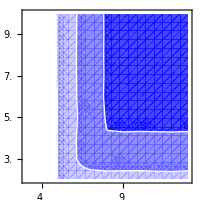

pathOut/regionPlotTZ.pdf

```mathematica
regionPlotTZ = RegionPlot[
  {
    probabilityTZ[tdmax,zMax] < outSigma[1],
    probabilityTZ[tdmax,zMax] < outSigma[2],
    probabilityTZ[tdmax,zMax] < outSigma[3]
  },
  {tdmax, First@tdmaxValues, tdmax0}, {zMax, First@zMaxValues, zMax0},
  Background->White, 
  PlotStyle -> plotStyle,
  BoundaryStyle -> boundaryStyle,
  FrameStyle -> frameStyle,
  FrameTicksStyle -> frameTicksStyle,
  FrameTicks->{{frameTicksZ, frameTicksZ},{frameTicksTmax, frameTicksTmax}},
  PlotRangePadding->None,
  ImagePadding->{{None, None}, {None, None}},
  ImageSize->{plotSize, plotSize},
  PlotRange->{{First@tdmaxValues, tdmax0}, {First@zMaxValues, zMax0}}
]

exportOut["regionPlotTZ.pdf", regionPlotTZ]
```

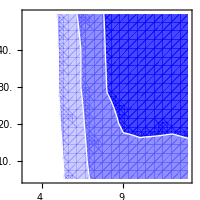

pathOut/regionPlotTTmin.pdf

```mathematica
regionPlotTTmin = RegionPlot[
  {
    probabilityTTmin[tdmax,tdmin] < outSigma[1],
    probabilityTTmin[tdmax,tdmin] < outSigma[2],
    probabilityTTmin[tdmax,tdmin] < outSigma[3]
  },
  {tdmax, First@tdmaxValues, tdmax0}, {tdmin, First@tdminValues, tdmin0},
  Background->White, 
  PlotStyle -> plotStyle,
  BoundaryStyle -> boundaryStyle,
  FrameStyle -> frameStyle,
  FrameTicksStyle -> frameTicksStyle,
  PlotRangePadding->None,
  FrameTicks->{{frameTicksTmin, frameTicksTmin},{frameTicksTmax, frameTicksTmax}},
  ImagePadding->{{None, None}, {spaceBottom, None}},
  ImageSize->{plotSize, plotSize + spaceBottom},
  PlotRange->{{First@tdmaxValues, tdmax0}, {First@tdminValues, tdmin0}}
]

exportOut["regionPlotTTmin.pdf", regionPlotTTmin]
```

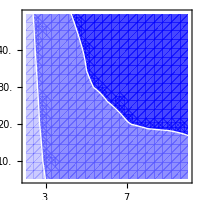

pathOut/regionPlotZTmin.pdf

```mathematica
regionPlotZTmin = RegionPlot[
  {
    probabilityZTmin[zMax,tdmin] < outSigma[1],
    probabilityZTmin[zMax,tdmin] < outSigma[2],
    probabilityZTmin[zMax,tdmin] < outSigma[3]
  },
  {zMax, First@zMaxValues, zMax0}, {tdmin, First@tdminValues, tdmin0},
  Background->White, 
  PlotStyle -> plotStyle,
  BoundaryStyle -> boundaryStyle,
  FrameStyle -> frameStyle,
  FrameTicksStyle -> frameTicksStyle,
  FrameTicks->{{frameTicksTmin, frameTicksTmin},{frameTicksZ, frameTicksZ}},
  PlotRangePadding->None,
  ImagePadding->{{None, None}, {spaceBottom, None}},
  ImageSize->{plotSize, plotSize + spaceBottom},
  PlotRange->{{First@zMaxValues, zMax0}, {First@tdminValues, tdmin0}}
]

exportOut["regionPlotZTmin.pdf", regionPlotZTmin]
```

```mathematica
cornerPlotGBH = Grid[
  {
    {regionPlotKT}, 
    {regionPlotKZ, regionPlotTZ}, 
    {regionPlotKTmin, regionPlotTTmin, regionPlotZTmin}
  }, 
  Spacings -> {0,0}, 
  Background->White
]

exportOut["cornerPlotGBH.jpg", cornerPlotGBH]; (*jpg export*)
(*The PDF export generate strange thin lines between the plots. Don't know how to solve it. 
Alternative: use ResourceFunction["PlotGrid"] (https://resources.wolframcloud.com/FunctionRepository/resources/PlotGrid/). 
It does not require doing each one of the plots individually and cropping the numbers, 
but if the above plots are used, it does not work well.*)
```

-Graphics- |  | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

## Confidence plots DEBH approach

```mathematica
baseSimPoints = 2 10^5; (*10^5 is sufficient here.*)

wValues = Select[listw, -0.6 >= # >= -1&]; 
tdmaxValues = Range[3, 13, 1];
tdminValues = {0.005, 0.01, 0.02, 0.03, 0.04, 0.05}; 
zMaxValues = Range[2, 10, 1];
```

### Computing... And defining the probabilities

Order: wT, wZ, wTmin,  TZ, TTmin, ZTmin

```mathematica
isComputeTable𝒟M1DEWT = False; (*Takes about 2 minutes with baseSimPoints = 2 10^5*)

If[isComputeTable𝒟M1DEWT, 
  Echo["Computing..."];
  table𝒟M1DEWT = Table[
    𝒟M1Formation[0.4, k-> -3 w1, w -> w1, tdmax-> tdmax1], 
    {w1, wValues}, 
    {tdmax1, tdmaxValues}
  ]; // EchoTiming;
  dumpsave["tableDM1DEWT.mx", table𝒟M1DEWT],
  (*else*)
  getAux["tableDM1DEWT.mx"];
  Echo["table𝒟M1DEWT loaded."];
];

tableProbDEWT = Block[
  {probAux},
  probAux[nw1_, nt1_] := NProbability[x>2, x \[Distributed] table𝒟M1DEWT[[nw1, nt1]]]^72;
  ParallelTable[
    {{wValues[[nw]], tdmaxValues[[nt]]}, probAux[nw, nt]}, 
    {nw, Length @ wValues}, 
    {nt, Length @ tdmaxValues} 
  ]
]; // AbsoluteTiming
probabilityDEWT[w_, tdmax_] = Interpolation[Flatten[tableProbDEWT,1], InterpolationOrder -> 2][w, tdmax];
```

Computing...

0.017886

{6.99252,Null}

```mathematica
isComputeTable𝒟M1DEWZ = True; (*About 5-10 minutes with baseSimPoints = 2 10^5*)

If[isComputeTable𝒟M1DEWZ, 
  Echo["Computing..."];
  table𝒟M1DEWZ = Table[
    𝒟M1Formation[0.4, k-> - 3 w1, w -> w1, zMax-> zMax1], 
    {w1, wValues}, 
    {zMax1, zMaxValues}
  ]; // EchoTiming;
  dumpsave["tableDM1DEWZ.mx", table𝒟M1DEWZ],
  (*else*)
  getAux["tableDM1DEWZ.mx"];
  Echo["table𝒟M1DEWZ loaded."];
];

tableProbDEWZ = Block[
  {probAux},
  probAux[n_, m_] := NProbability[x>2, x \[Distributed] table𝒟M1DEWZ[[n, m]]]^72;
  ParallelTable[
    {{wValues[[n]], zMaxValues[[m]]}, probAux[n, m]}, 
    {n, Length @ wValues}, 
    {m, Length @ zMaxValues} 
  ]
]; // AbsoluteTiming
probabilityDEWZ[w_, zMax_] = Interpolation[Flatten[tableProbDEWZ,1], InterpolationOrder -> 2][w, zMax];
```

{8.2082,Null}

```mathematica
isComputeTable𝒟M1DEWTmin = True;

If[isComputeTable𝒟M1DEWTmin, 
  Echo["Computing..."];
  table𝒟M1DEWTmin = Table[
    𝒟M1Formation[0.4, k-> - 3 w1, w-> w1, tdmin-> tdmin1], 
    {w1, wValues}, 
    {tdmin1, tdminValues}
  ]; // EchoTiming;
  dumpsave["tableDM1DEWTmin.mx", table𝒟M1DEWTmin],
  (*else*)
  getAux["tableDM1DEWTmin.mx"];
  Echo["table𝒟M1DEWTmin loaded."];
];

tableProbDEWTmin = Block[
  {probAux},
  probAux[n_, m_] := NProbability[x>2, x \[Distributed] table𝒟M1DEWTmin[[n, m]]]^72;
  ParallelTable[
    {{wValues[[n]], tdminValues[[m]]}, probAux[n, m]}, 
    {n, Length @ wValues}, 
    {m, Length @ tdminValues} 
  ]
]; // AbsoluteTiming
probabilityDEWTmin[w_, tdmin_] = Interpolation[Flatten[tableProbDEWTmin,1], InterpolationOrder -> 2][w, tdmin];
```

Computing...

0.018403

{5.22842,Null}

```mathematica
isComputeTable𝒟M1DETZ = True;

If[isComputeTable𝒟M1DETZ, 
  Echo["Computing..."];
  table𝒟M1DETZ = Table[
    𝒟M1Formation[0.4, tdmax-> tdmax1, zMax-> zMax1], 
    {tdmax1, tdmaxValues}, 
    {zMax1, zMaxValues}
  ]; // EchoTiming;
  dumpsave["tableDM1DETZ.mx", table𝒟M1DETZ],
  (*else*)
  getAux["tableDM1DETZ.mx"];
  Echo["table𝒟M1DETZ loaded."];
];

tableProbDETZ = Block[
  {probAux},
  probAux[n_, m_] := NProbability[x>2, x \[Distributed] table𝒟M1DETZ[[n, m]]]^72;
  ParallelTable[
    {{tdmaxValues[[n]], zMaxValues[[m]]}, probAux[n, m]}, 
    {n, Length @ tdmaxValues}, 
    {m, Length @ zMaxValues} 
  ]
]; // AbsoluteTiming
probabilityDETZ[tdmax_, zMax_] = Interpolation[Flatten[tableProbDETZ,1], InterpolationOrder -> 2][tdmax, zMax];
```

Computing...

0.021843

{10.3195,Null}

```mathematica
isComputeTable𝒟M1DETTmin = True;

If[isComputeTable𝒟M1DETTmin, 
  Echo["Computing..."];
  table𝒟M1DETTmin = Table[
    𝒟M1Formation[0.4, tdmax-> tdmax1, tdmin-> tdmin1], 
    {tdmax1, tdmaxValues}, 
    {tdmin1, tdminValues}
  ]; // EchoTiming;
  dumpsave["tableDM1DETTmin.mx", table𝒟M1DETTmin],
  (*else*)
  getAux["tableDM1DETTmin.mx"];
  Echo["table𝒟M1DETTmin loaded."];
];

tableProbDETTmin = Block[
  {probAux},
  probAux[n_, m_] := NProbability[x>2, x \[Distributed] table𝒟M1DETTmin[[n, m]]]^72;
  ParallelTable[
    {{tdmaxValues[[n]], tdminValues[[m]]}, probAux[n, m]}, 
    {n, Length @ tdmaxValues}, 
    {m, Length @ tdminValues} 
  ]
]; // AbsoluteTiming
probabilityDETTmin[tdmax_, tdmin_] = Interpolation[Flatten[tableProbDETTmin,1], InterpolationOrder -> 2][tdmax, tdmin];
```

Computing...

0.030591

{9.85212,Null}

```mathematica
isComputeTable𝒟M1DEZTmin = True;

If[isComputeTable𝒟M1DEZTmin, 
  Echo["Computing..."];
  table𝒟M1DEZTmin = Table[
    𝒟M1Formation[0.4, zMax-> zMax1, tdmin-> tdmin1], 
    {zMax1, zMaxValues}, 
    {tdmin1, tdminValues}
  ]; // EchoTiming;
  dumpsave["tableDM1DEZTmin.mx", table𝒟M1DEZTmin],
  (*else*)
  getAux["tableDM1DEZTmin.mx"];
  Echo["table𝒟M1DEZTmin loaded."];
];

tableProbDEZTmin = Block[
  {probAux},
  probAux[n_, m_] := NProbability[x>2, x \[Distributed] table𝒟M1DEZTmin[[n, m]]]^72;
  ParallelTable[
    {{zMaxValues[[n]], tdminValues[[m]]}, probAux[n, m]}, 
    {n, Length @ zMaxValues}, 
    {m, Length @ tdminValues} 
  ]
]; // AbsoluteTiming
probabilityDEZTmin[zMax_, tdmin_] = Interpolation[Flatten[tableProbDEZTmin,1], InterpolationOrder -> 2][zMax, tdmin];
```

Computing...

242.961

{8.91649,Null}

### Plots

Order: WT, WZ, WTmin,  TZ, TTmin, ZTmin

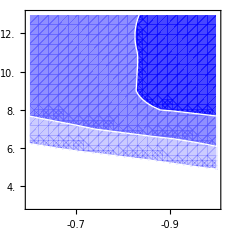

pathOut/regionPlotDEWT.pdf

```mathematica
largeTick = 0.02;
smallTick = 0.01;
frameTicksW = Table[If[IntegerPart[i]==i, {i/10., i/10., largeTick}, {i/10., "", smallTick}], {i, -9.5, -6.0, 0.5}];
frameTicksZ = Table[If[IntegerPart[i]==i, {i, i, largeTick}, {i, "", smallTick}], {i, 2.5, 9.5, 0.5}];
frameTicksTmin = Table[If[IntegerPart[i]==i, {i/100, i 10 (*Myr unit*), largeTick}, {i/100, "", smallTick}], {i, 0.5, 4.5, 0.5}];
frameTicksTmax = Table[If[IntegerPart[i]==i, {i, i, largeTick}, {i, "", smallTick}], {i, 3.5, 12.5, 0.5}];

plotSize = 200;
spaceLeft = 30;
spaceBottom = 20;
frameStyle = Directive[Black, FontSize -> 18, Thickness[0.005]];
frameTicksStyle = Directive[Black, FontFamily-> "Times"];
boundaryStyle = {1 -> Directive[White, Thin], 2 -> Directive[White, Thin], 3-> Directive[White, Thin]};
plotStyle = {Directive[Lighter@Blue, Opacity[0.3]], Directive[Lighter@Blue, Opacity[0.5]], Directive[Blue, Opacity[0.5]]};

regionPlotDEWT = RegionPlot[
  {
    probabilityDEWT[w,tdmax] < outSigma[1],
    probabilityDEWT[w,tdmax] < outSigma[2],
    probabilityDEWT[w,tdmax] < outSigma[3]
  },
  {w,-1, -0.6}, {tdmax, First@tdmaxValues, tdmax0},
  Background -> White, 
  PlotStyle -> plotStyle,
  BoundaryStyle -> boundaryStyle,
  FrameStyle -> frameStyle,
  FrameTicksStyle -> frameTicksStyle,
  FrameTicks -> {{frameTicksTmax, frameTicksTmax}, {frameTicksW, frameTicksW}},
  PlotRangePadding -> None,
  PlotRange -> {{-0.6,-1}, {First@tdmaxValues, tdmax0}},
  ImagePadding -> {{spaceLeft, None}, {None, None}},
  ImageSize -> {plotSize + spaceLeft, plotSize},
  ScalingFunctions -> {"Reverse", Identity}
]

exportOut["regionPlotDEWT.pdf", regionPlotDEWT]
```

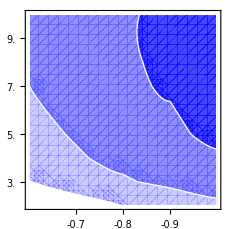

pathOut/regionPlotDEWZ.pdf

```mathematica
regionPlotDEWZ = RegionPlot[
  {
    probabilityDEWZ[w,zMax] < outSigma[1],
    probabilityDEWZ[w,zMax] < outSigma[2],
    probabilityDEWZ[w,zMax] < outSigma[3]
  },
  {w, -0.6, -1}, {zMax, First@zMaxValues, zMax0},
  Background->White, 
  PlotStyle -> plotStyle,
  BoundaryStyle -> boundaryStyle,
  FrameStyle -> frameStyle,
  FrameTicksStyle -> frameTicksStyle,
  FrameTicks->{{frameTicksZ, frameTicksZ}, {frameTicksW, frameTicksW}},
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotRangePadding->None,
  ImagePadding->{{spaceLeft, None}, {None, None}},
  ImageSize->{plotSize + spaceLeft, plotSize},
  PlotRange->{{-1, -0.6}, {First@zMaxValues, zMax0}},
  ScalingFunctions -> {"Reverse", Identity}
]

exportOut["regionPlotDEWZ.pdf", regionPlotDEWZ]
```

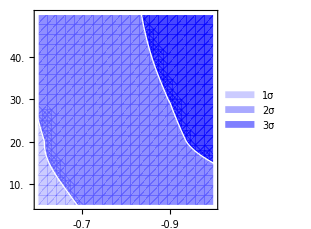

pathOut/regionPlotDEWTmin.pdf

```mathematica
regionPlotDEWTmin = RegionPlot[
  {
    probabilityDEWTmin[w,tdmin] < outSigma[1],
    probabilityDEWTmin[w,tdmin] < outSigma[2],
    probabilityDEWTmin[w,tdmin] < outSigma[3]
  },
  {w, -0.6, -1}, {tdmin, First@tdminValues, tdmin0},
  Background->White, 
  PlotStyle -> plotStyle,
  BoundaryStyle -> boundaryStyle,
  FrameStyle -> frameStyle,
  FrameTicksStyle -> frameTicksStyle,
  FrameTicks -> {{frameTicksTmin, frameTicksTmin},{frameTicksW, frameTicksW}},
  PlotRangePadding -> None,
  ImagePadding->{{spaceLeft, None}, {spaceBottom, None}},
  ImageSize->{plotSize + spaceLeft, plotSize + spaceBottom},
  PlotLegends -> Placed[{
    Style["1σ", FontFamily->"Times", FontSize -> 18], 
    Style["2σ", FontFamily->"Times", FontSize -> 18], 
    Style["3σ", FontFamily->"Times", FontSize -> 18]}, 
    {0.15, 0.18}
  ],
  PlotRange->{{-1,-0.6}, {First@tdminValues, tdmin0}},
  ScalingFunctions -> {"Reverse", Identity}
]

exportOut["regionPlotDEWTmin.pdf", regionPlotDEWTmin]
```

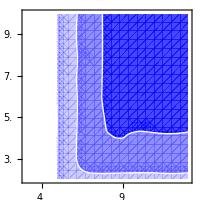

pathOut/regionPlotDETZ.pdf

```mathematica
regionPlotDETZ = RegionPlot[
  {
    probabilityDETZ[tdmax,zMax] < outSigma[1],
    probabilityDETZ[tdmax,zMax] < outSigma[2],
    probabilityDETZ[tdmax,zMax] < outSigma[3]
  },
  {tdmax, First@tdmaxValues, tdmax0}, {zMax, First@zMaxValues, zMax0},
  Background->White, 
  PlotStyle -> plotStyle,
  BoundaryStyle -> boundaryStyle,
  FrameStyle -> frameStyle,
  FrameTicksStyle -> frameTicksStyle,
  FrameTicks->{{frameTicksZ, frameTicksZ},{frameTicksTmax, frameTicksTmax}},
  PlotRangePadding->None,
  ImagePadding->{{None, None}, {None, None}},
  ImageSize->{plotSize, plotSize},
  PlotRange->{{First@tdmaxValues, tdmax0}, {First@zMaxValues, zMax0}}
]

exportOut["regionPlotDETZ.pdf", regionPlotDETZ]
```

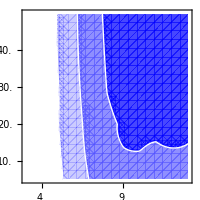

pathOut/regionPlotDETTmin.pdf

```mathematica
regionPlotDETTmin = RegionPlot[
  {
    probabilityDETTmin[tdmax,tdmin] < outSigma[1],
    probabilityDETTmin[tdmax,tdmin] < outSigma[2],
    probabilityDETTmin[tdmax,tdmin] < outSigma[3]
  },
  {tdmax, First@tdmaxValues, tdmax0}, {tdmin, First@tdminValues, tdmin0},
  Background->White, 
  PlotStyle -> plotStyle,
  BoundaryStyle -> boundaryStyle,
  FrameStyle -> frameStyle,
  FrameTicksStyle -> frameTicksStyle,
  PlotRangePadding->None,
  FrameTicks->{{frameTicksTmin, frameTicksTmin},{frameTicksTmax, frameTicksTmax}},
  ImagePadding->{{None, None}, {spaceBottom, None}},
  ImageSize->{plotSize, plotSize + spaceBottom},
  PlotRange->{{First@tdmaxValues, tdmax0}, {First@tdminValues, tdmin0}}
]

exportOut["regionPlotDETTmin.pdf", regionPlotDETTmin]
```

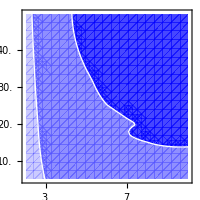

pathOut/regionPlotDEZTmin.pdf

```mathematica
regionPlotDEZTmin = RegionPlot[
  {
    probabilityDEZTmin[zMax,tdmin] < outSigma[1],
    probabilityDEZTmin[zMax,tdmin] < outSigma[2],
    probabilityDEZTmin[zMax,tdmin] < outSigma[3]
  },
  {zMax, First@zMaxValues, zMax0}, {tdmin, First@tdminValues, tdmin0},
  Background->White, 
  PlotStyle -> plotStyle,
  BoundaryStyle -> boundaryStyle,
  FrameStyle -> frameStyle,
  FrameTicksStyle -> frameTicksStyle,
  FrameTicks->{{frameTicksTmin, frameTicksTmin},{frameTicksZ, frameTicksZ}},
  PlotRangePadding->None,
  ImagePadding->{{None, None}, {spaceBottom, None}},
  ImageSize->{plotSize, plotSize + spaceBottom},
  PlotRange->{{First@zMaxValues, zMax0}, {First@tdminValues, tdmin0}}
]

exportOut["regionPlotDEZTmin.pdf", regionPlotDEZTmin]
```

```mathematica
cornerPlotDEBH = Grid[
  {
    {regionPlotDEWT}, 
    {regionPlotDEWZ, regionPlotDETZ}, 
    {regionPlotDEWTmin, regionPlotDETTmin, regionPlotDEZTmin}
  }, 
  Spacings -> {0,0}, 
  Background->White
]

exportOut["cornerPlotDEBH.jpg", cornerPlotDEBH]; (*jpg export*)
```

-Graphics- |  | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

## Plots for the illustration with arrows

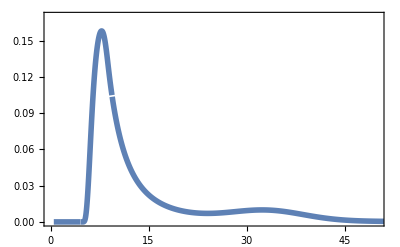

plotArrowsMerger.pdf

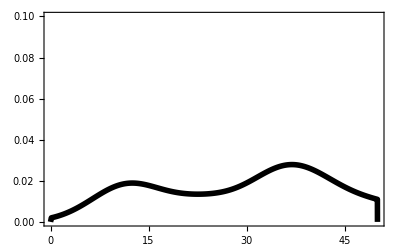

plotArrowsObs.pdf

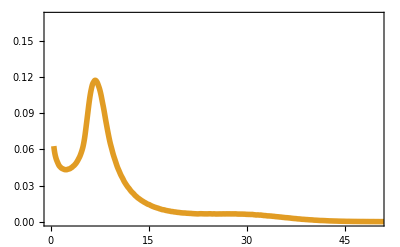

plotArrowsCCBH.pdf

```mathematica
plotArrowsMerger = Plot[
  {PDF[𝒟plp, x]}, 
  {x,0.5,100}, 
  PlotRange-> {{0,50}, {0,0.17}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotPoints->2700,
  MaxRecursion->0,
  PlotStyle->{{Thickness[0.01], ColorData[97, "ColorList"][[1]]}}
]

Export["plotArrowsMerger.pdf", plotArrowsMerger]

plotArrowsObs = SmoothHistogram[
  mXzDataForPlotting[[All,2]] /. Around[x_,y_] ->  x, 
  5, 
  "PDF",  
  PlotRange->{{0,50}, {0,.10}}, 
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotStyle->{{Thickness[0.01], Black}}
]

Export["plotArrowsObs.pdf", plotArrowsObs]

plotArrowsCCBH = Plot[
  {PDF[𝒟m1Formation, x]}, 
  {x,0.5,100}, 
  PlotRange-> {{0,50}, {0,0.17}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotPoints->2700,
  MaxRecursion->0,
  PlotStyle->{{Thickness[0.01], ColorData[97, "ColorList"][[2]]}}
]

Export["plotArrowsCCBH.pdf", plotArrowsCCBH]
```

```mathematica
Plot[PDF[𝒟M1Formation[0.4], x], {x, 0,100}]
```

DataDistribution[<<SmoothKernel>>, {199307}]

## Formation mass distribution straight from observational data

```mathematica
Clear[dataM1ObsFormation];
mXzDataCentralValues = mXzDataForPlotting /. Around[x_, y_] -> x;

dataM1ObsFormation[k_, w_] := dataM1ObsFormation[k, w] =  #2 RandomVariate[𝒟InvMassFactor[#1, k, w], 10^5] &  @@@ mXzDataCentralValues;
```

```mathematica
dataM1ObsFormation[k0, w0] // EchoTiming; (*Check if it indeed has to be so long this computation*)
```

156.571

```mathematica
dataM1ObsFormationk0w0 = dataM1ObsFormation[k0, w0];
DumpSave["dataM1ObsFormationk0w0.mx", dataM1ObsFormationk0w0];
```

```mathematica
dataM1ObsFormation[k0, w0] // EchoTiming;

histFormationDistTest = Histogram[
  dataM1ObsFormation[k0, w0], 
  {0.4}, 
  "PDF", 
  PlotRange->{{0,100}, All},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"]
]
```

3.×10^-6

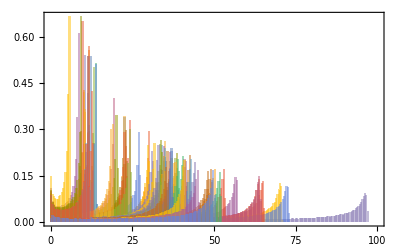

```mathematica
Clear[𝒟M1ObsFormation];
𝒟M1ObsFormation[bhNumber_, k_, w_] := 𝒟M1ObsFormation[bhNumber, k, w] = SmoothKernelDistribution[
  dataM1ObsFormation[k, w][[bhNumber]],
  0.1, 
  InterpolationPoints -> 10^5, 
  MaxExtraBandwidths -> {0,0}, 
  PerformanceGoal->"Quality"
]
```

```mathematica
𝒟M1ObsFormation[#, k0, w0] & /@ Range[72] // EchoTiming;
```

24.3162

```mathematica
PDF[𝒟M1ObsFormation[1, k0, w0], 20]
```

0.0142567

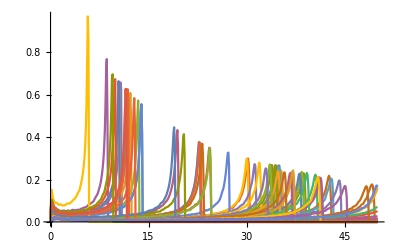

```mathematica
Block[
  {list = Table[{#, PDF[𝒟M1ObsFormation[i, k0, w0], #]} & /@ Range[0, 50, 0.1], {i,72}]},
  ListPlot[list, Joined->True, PlotRange->All]
]
```

```mathematica
probabilityGoodMass[bhNumber_, minimumMass_] := NProbability[m1 > minimumMass, m1 \[Distributed] 𝒟M1ObsFormation[bhNumber, k0, w0]];

totalProbabilityGoodMass[minimumMass_] := Product[probabilityGoodMass[bhNumber, minimumMass], {bhNumber, 1, 72}];
```

```mathematica
totalProbabilityGoodMass[2]
```

0.0101338

```mathematica
FindRoot[NProbability[Abs[x] > x0, x\[Distributed]NormalDistribution[]]==0.01 , {x0 , 2}]
```

{x0→2.57583}